

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
x-7==19+x
```

-7+x==19+x

```mathematica
Solve[-7+x==19+x,{x}]
```

{}

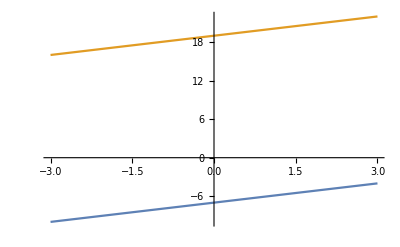

```mathematica
Plot[{x-7,19+x},{x,-3,3}]
```

```mathematica
-7+x==19+x/.x->∞
```

True

```mathematica
Union[Reals,{∞}]
```

Union::normal: Nonatomic expression expected at position 1 in ∪{∞}.

ℝ∪{∞}

```mathematica
Solve[-7+x==19+x,x,Union[Reals,{∞}]]
```

Union::normal: Nonatomic expression expected at position 1 in ∪{∞}.

Solve::bdomv: Warning: ∪{∞} is not a valid domain specification. Assuming it is a variable to eliminate.

{}

```mathematica
Graphics3D[Pyramid[]]
```

-Graphics3D-

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

```mathematica
Graphics3D[Dodecahedron[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cube[]]
```

-Graphics3D-

```mathematica
Graphics3D[Tetrahedron[]]
```

-Graphics3D-

```mathematica
Plot[x,{x,-2,2}]
```

-Graphics-



```mathematica
Plot[x^2,{x,-2,2}]
```

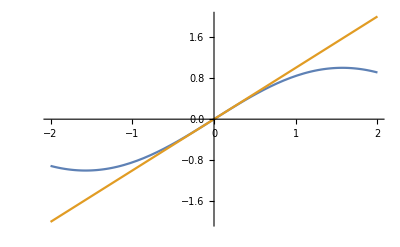

```mathematica
Plot[{Sin[x],x},{x,-2,2}]
```

```mathematica
Manipulate[
Plot[{Sin[x],0,a Sin[x]},{x,-2,2},PlotRange->{-2,2}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[
{Sin[x],0,a Sin[x]}
,{x,-2π,2π}
,PlotRange->{-2,2}]
,{a,0,1}]
```

```mathematica
{1,0}.Normalize[{1,1}]
```

1/(√2)

```mathematica
RootOfUnityQ[1/(√2)]
```

False

```mathematica
AlgebraicUnitQ[1/(√2)]
```

False

```mathematica
AlgebraicIntegerQ[1/(√2)]
```

False

```mathematica
AlgebraicNumberDenominator[1/(√2)]
```

2

```mathematica
AlgebraicNumberNorm[1/(√2)]
```

-1/2

```mathematica
AlgebraicNumberTrace[1/(√2)]
```

0

```mathematica
ToNumberField[1/(√2)]
```

AlgebraicNumber0.707AlgebraicNumber[√2,{0,1/2}]0.7071067811865476

```mathematica
IsolatingInterval[1/(√2)]
```

{45/64,91/128}

```mathematica
MinimalPolynomial[1/(√2),x]
```

-1+2 x^2

```mathematica
{x,Sin[x]}.RotationMatrix[2π-π/4]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

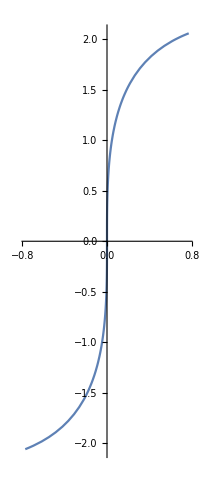

```mathematica
ParametricPlot[
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
,{x,-2,2}]
```

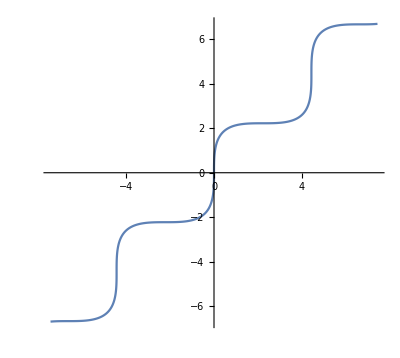

```mathematica
ParametricPlot[
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
,{x,-10,10}]
```

```mathematica
Integrate[√(1+4 x^2),{x,0,1}]
```

1/4 (2 √5+ArcSinh[2])

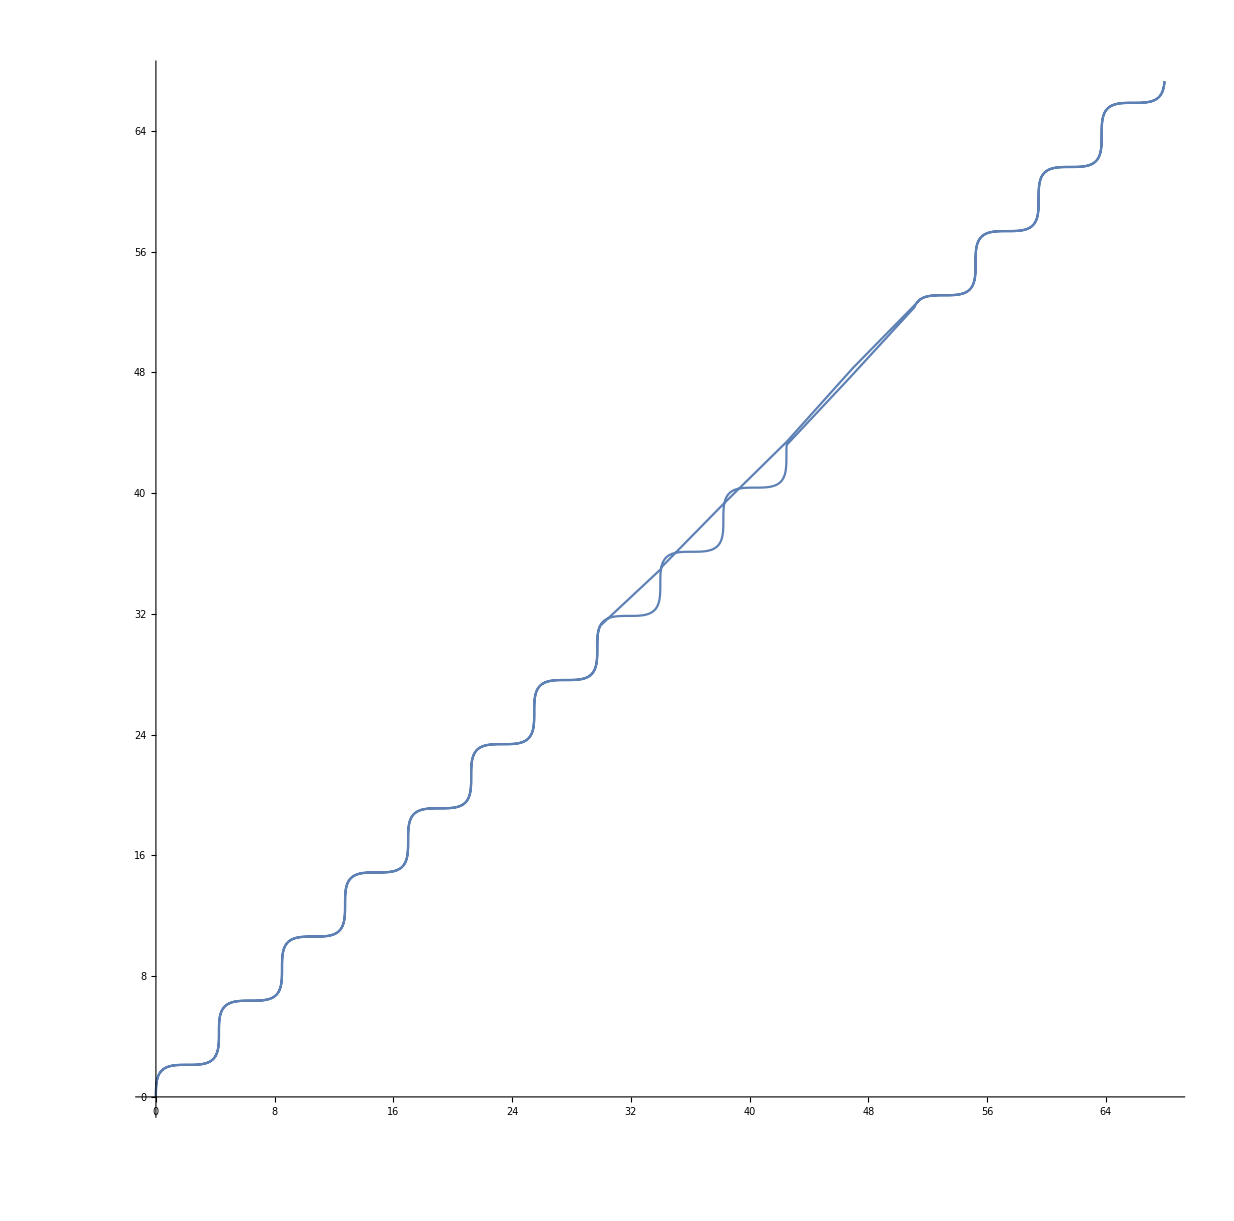

```mathematica
With[{f=Function[x,x^2]},
With[{len=Integrate[√(1+f'[x]^2),{x,0,1}]},
ParametricPlot[
{f[x]/len-Sin[f[x]]/len,f[x]/len+Sin[f[x]]/len}
,{x,-10,10}]
]]
```

```mathematica
FullSimplify[ArcCurvature[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x],x∈Reals]
```

Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

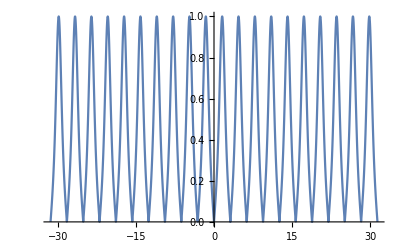

```mathematica
Plot[Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,-10 π,10 π}]
```

```mathematica
Integrate[Sin[x],{x,0,2π}]
```

0

```mathematica
Norm@D[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x]
```

√(Abs[1/(√2)-Cos[x]/(√2)]^2+Abs[1/(√2)+Cos[x]/(√2)]^2)

```mathematica
FullSimplify[√(Abs[1/(√2)-Cos[x]/(√2)]^2+Abs[1/(√2)+Cos[x]/(√2)]^2),x∈Reals]
```

(√(3+Cos[2 x]))/(√2)

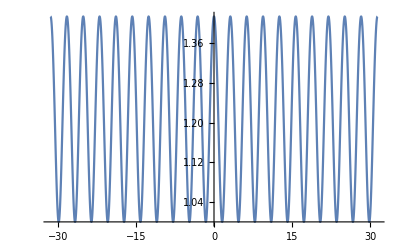

```mathematica
Plot[(√(3+Cos[2 x]))/(√2),{x,-10 π,10 π}]
```

```mathematica
f[x]=={x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
```

f[x]=={x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

```mathematica
FullSimplify[{x,Sin[x]}.RotationMatrix[π/4],x∈Reals]
```

{(x+Sin[x])/(√2),(-x+Sin[x])/(√2)}

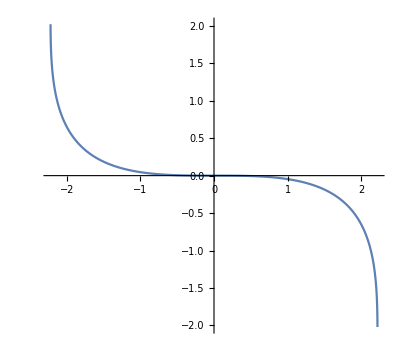

```mathematica
ParametricPlot[
{(x+Sin[x])/(√2),(-x+Sin[x])/(√2)}
,{x,-3,3}]
```

```mathematica
ParametricPlot[
{(x+Sin[x])/(√2),(-x+Sin[x])/(√2)}
,{x,-3,3}]
```

```mathematica
{x,x}=={x,4x}.RotationMatrix[θ]
```

{x,x}=={x Cos[θ]+4 x Sin[θ],4 x Cos[θ]-x Sin[θ]}

```mathematica
Reduce[{x,x}=={x Cos[θ]+4 x Sin[θ],4 x Cos[θ]-x Sin[θ]}]
```

(Sin[θ]==3/17&&Cos[θ]==5/17)||x==0

```mathematica
Reduce[{x,x}=={x Cos[θ]+4 x Sin[θ],4 x Cos[θ]-x Sin[θ]},θ]
```

x==0

```mathematica
Solve[{x==x Cos[θ]+4 x Sin[θ],x==4 x Cos[θ]-x Sin[θ]},θ,Reals]
```

{}

```mathematica
Solve[{x==x Cos[θ]+4 x Sin[θ],x==4 x Cos[θ]-x Sin[θ]},θ,]
```

Solve::bdomv: Warning: Null is not a valid domain specification. Assuming it is a variable to eliminate.

{}

```mathematica
Solve[{x==x Cos[θ]+4 x Sin[θ],x==4 x Cos[θ]-x Sin[θ]},θ]
```

{}

```mathematica
(Sin[θ]==3/17&&Cos[θ]==5/17)
```

Sin[θ]==3/17&&Cos[θ]==5/17

```mathematica
FindInstance[Sin[θ]==3/17&&Cos[θ]==5/17,{θ}]
```

{}

```mathematica
Cos[θ]==5/17
```

Cos[θ]==5/17

```mathematica
FindInstance[Cos[θ]==5/17,{θ}]
```

{{θ→-48 π-ArcCos[5/17]}}

```mathematica
FullSimplify[{x,Sin[x]}.RotationMatrix[-48 π-ArcCos[5/17]],x∈Reals]
```

{1/17 (5 x-2 √66 Sin[x]),1/17 (2 √66 x+5 Sin[x])}

```mathematica
FullSimplify[ArcCurvature[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x],x∈Reals]
```

Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

```mathematica
Plot[Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,-10 π,10 π}]
```

-Graphics-

```mathematica
FullSimplify[ArcCurvature[{x,Sin[x]},x],x∈Reals]
```

Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

```mathematica
FullSimplify[ArcCurvature[{g[x],f[x]},x],{x,g[x],f[x]}∈Reals]==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))
```

√((g'[x] f''[x]-f'[x] g''[x])^2/((f'[x]^2+g'[x]^2)^3))==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

```mathematica
DSolve[√((g'[x] f''[x]-f'[x] g''[x])^2/((f'[x]^2+g'[x]^2)^3))==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{f[x],g[x],f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[√((g'[x] f''[x]-f'[x] g''[x])^2/((f'[x]^2+g'[x]^2)^3))==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{f[x],g[x],f[x],g[x]},{x}]

```mathematica
DSolve[√((g'[x] f''[x]-f'[x] g''[x])^2/((f'[x]^2+g'[x]^2)^3))==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{f[x]},{x}]
```

$Aborted

```mathematica
ParametricPlot[
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
,{x,-10,10}]
```

-Graphics-

```mathematica
D[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x]
```

{1/(√2)-Cos[x]/(√2),1/(√2)+Cos[x]/(√2)}

```mathematica
D[{1/(√2)-Cos[x]/(√2),1/(√2)+Cos[x]/(√2)},x]
```

{Sin[x]/(√2),-Sin[x]/(√2)}

```mathematica
Integrate[{Sin[x]/(√2),-Sin[x]/(√2)},x,GeneratedParameters->C]
```

{C[1]-Cos[x]/(√2),C[1]+Cos[x]/(√2)}

```mathematica
Integrate[Integrate[{Sin[x]/(√2),-Sin[x]/(√2)},x,GeneratedParameters->C],x,GeneratedParameters->C]
```

{x C[1]+C[2]-Sin[x]/(√2),x C[1]+C[2]+Sin[x]/(√2)}

```mathematica
D[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x]
```

{1/(√2)-Cos[x]/(√2),1/(√2)+Cos[x]/(√2)}

```mathematica
Integrate[{1/(√2)-Cos[x]/(√2),1/(√2)+Cos[x]/(√2)},x,GeneratedParameters->C]
```

{C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)}

```mathematica
{x C[1]+C[2]-Sin[x]/(√2),x C[1]+C[2]+Sin[x]/(√2)}=={C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)}
```

{x C[1]+C[2]-Sin[x]/(√2),x C[1]+C[2]+Sin[x]/(√2)}=={C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)}

```mathematica
Solve[{x C[1]+C[2]-Sin[x]/(√2),x C[1]+C[2]+Sin[x]/(√2)}=={C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)},{ C[1], C[2]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C[2]→x/(√2)-(-1+x) C[1]}}

```mathematica
{x C[1]+C[2]-Sin[x]/(√2),x C[1]+C[2]+Sin[x]/(√2)}=={C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)}/.{C[2]->x/(√2)-(-1+x) C[1]}
```

{x/(√2)-(-1+x) C[1]+x C[1]-Sin[x]/(√2),x/(√2)-(-1+x) C[1]+x C[1]+Sin[x]/(√2)}=={C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)}

```mathematica
{x/(√2)-(-1+x) C[1]+x C[1]-Sin[x]/(√2),x/(√2)-(-1+x) C[1]+x C[1]+Sin[x]/(√2)}=={C[1]+√2 (x/2-Sin[x]/2),C[1]+(x+Sin[x])/(√2)}/.x->f[x]
```

{-C[1] (-1+f[x])+f[x]/(√2)+C[1] f[x]-Sin[f[x]]/(√2),-C[1] (-1+f[x])+f[x]/(√2)+C[1] f[x]+Sin[f[x]]/(√2)}=={C[1]+√2 (f[x]/2-1/2 Sin[f[x]]),C[1]+(f[x]+Sin[f[x]])/(√2)}

```mathematica
Reduce[{-C[1] (-1+f[x])+f[x]/(√2)+C[1] f[x]-Sin[f[x]]/(√2),-C[1] (-1+f[x])+f[x]/(√2)+C[1] f[x]+Sin[f[x]]/(√2)}=={C[1]+√2 (f[x]/2-1/2 Sin[f[x]]),C[1]+(f[x]+Sin[f[x]])/(√2)}]
```

True

```mathematica
Solve[{-C[1] (-1+f[x])+f[x]/(√2)+C[1] f[x]-Sin[f[x]]/(√2),-C[1] (-1+f[x])+f[x]/(√2)+C[1] f[x]+Sin[f[x]]/(√2)}=={C[1]+√2 (f[x]/2-1/2 Sin[f[x]]),C[1]+(f[x]+Sin[f[x]])/(√2)},f[x]]
```

{{}}

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x]==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),x∈Reals]
```

((1+Cos[x]^2)^3 f''[x]^2)/((1+f'[x]^2)^3)==Sin[x]^2

```mathematica
DSolve[((1+Cos[x]^2)^3 f''[x]^2)/((1+f'[x]^2)^3)==Sin[x]^2,{f[x],f[x]},{x}]
```

$Aborted

```mathematica
ExpandAll@(((1+Cos[x]^2)^3 f''[x]^2)/((1+f'[x]^2)^3))
```

f''[x]^2/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)+(3 Cos[x]^2 f''[x]^2)/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)+(3 Cos[x]^4 f''[x]^2)/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)+(Cos[x]^6 f''[x]^2)/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)

```mathematica
TrigReduce[%75]
```

(126 f''[x]^2+111 Cos[2 x] f''[x]^2+18 Cos[4 x] f''[x]^2+Cos[6 x] f''[x]^2)/(32 (1+f'[x]^2)^3)

```mathematica
FullSimplify[f''[x]^2/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)+(3 Cos[x]^2 f''[x]^2)/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)+(3 Cos[x]^4 f''[x]^2)/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)+(Cos[x]^6 f''[x]^2)/(1+3 f'[x]^2+3 f'[x]^4+f'[x]^6)==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,f[x],f'[x],f''[x]}∈Reals]
```

512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4

```mathematica
DSolve[512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,{f[x],f[x]},{x}]
```

$Aborted

```mathematica
NDSolve[512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,{f[x]},{x,-10,10}]
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,{f[x]},{x,-10,10}]

```mathematica
NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f[0]==0},{f[x]},{x,-10,10}]
```

NDSolve::ndnco: The number of constraints (1) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f[0]==0},{f[x]},{x,-10,10}]

```mathematica
I^I
```

ⅈ^ⅈ

```mathematica
N[ⅈ^ⅈ]
```

0.20788+0. ⅈ

```mathematica
NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f[0]==0},f,{x,-10,10}]
```

NDSolve::ndnco: The number of constraints (1) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f[0]==0},f,{x,-10,10}]

```mathematica
NDSolve[512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f,{x,-10,10}]
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f,{x,-10,10}]

```mathematica
NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4},f,{x,-10,10}]
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4},f,{x,-10,10}]

```mathematica
NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f[0]==0,f[2π]==0},f,{x,-10,10}]
```

NDSolve::ndsz: At x == 1.92538, step size is effectively zero; singularity or stiff system suspected.

NDSolve[{512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4,f[0]==0,f[2 π]==0},f,{x,-10,10}]

```mathematica
512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4/.f->Sin[x]
```

512 Sin[x]^2 (1+(Sin[x]'[x])^2)^6==(3+Cos[2 x])^9 (Sin[x]''[x])^4

```mathematica
With[{f=Sin},
512 Sin[x]^2 (1+f'[x]^2)^6==(3+Cos[2 x])^9 f''[x]^4
]
```

512 (1+Cos[x]^2)^6 Sin[x]^2==(3+Cos[2 x])^9 Sin[x]^4

```mathematica
Reduce[512 (1+Cos[x]^2)^6 Sin[x]^2==(3+Cos[2 x])^9 Sin[x]^4]
```

Cos[x]==-√(-1-√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,1]))||Cos[x]==√(-1-√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,1]))||Cos[x]==-√(-1+√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,1]))||Cos[x]==√(-1+√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,1]))||Cos[x]==-√(-1-√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,2]))||Cos[x]==√(-1-√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,2]))||Cos[x]==-√(-1+√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,2]))||Cos[x]==√(-1+√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,2]))||Cos[x]==-√(-1-√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,3]))||Cos[x]==√(-1-√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,3]))||Cos[x]==-√(-1+√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,3]))||Cos[x]==√(-1+√(1+Root[512-19683 Sin[x]^2-59049 Cos[2 x] Sin[x]^2-78732 Cos[2 x]^2 Sin[x]^2-61236 Cos[2 x]^3 Sin[x]^2-30618 Cos[2 x]^4 Sin[x]^2-10206 Cos[2 x]^5 Sin[x]^2-2268 Cos[2 x]^6 Sin[x]^2-324 Cos[2 x]^7 Sin[x]^2-27 Cos[2 x]^8 Sin[x]^2-Cos[2 x]^9 Sin[x]^2+1536 #1+1536 #1^2+512 #1^3&,3]))||Sin[x]==0

```mathematica
FullSimplify[512 (1+Cos[x]^2)^6 Sin[x]^2==(3+Cos[2 x])^9 Sin[x]^4,x∈Reals]
```

(3+Cos[2 x])^3 Sin[x]^3==8 Sin[x]

```mathematica
FullSimplify[ArcCurvature[{g[x],f[x]},x]==Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{f[x],g[x],x}∈Reals]
```

((1+Cos[x]^2)^3 (g'[x] f''[x]-f'[x] g''[x])^2)/((f'[x]^2+g'[x]^2)^3)==Sin[x]^2

```mathematica
DSolve[((1+Cos[x]^2)^3 (g'[x] f''[x]-f'[x] g''[x])^2)/((f'[x]^2+g'[x]^2)^3)==Sin[x]^2,{f[x],g[x],f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[((1+Cos[x]^2)^3 (g'[x] f''[x]-f'[x] g''[x])^2)/((f'[x]^2+g'[x]^2)^3)==Sin[x]^2,{f[x],g[x],f[x],g[x]},{x}]

```mathematica
TeXForm[((1+Cos[x]^2)^3 (g'[x] f''[x]-f'[x] g''[x])^2)/((f'[x]^2+g'[x]^2)^3)==Sin[x]^2]
```

\frac{\left(\cos ^2(x)+1\right)^3 \left(f''(x) g'(x)-f'(x) g''(x)\right)^2}{\left(f'(x)^2+g'(x)^2\right)^3}=\sin ^2(x)

```mathematica
With[{g=Identity,f=Sin},
((1+Cos[x]^2)^3 (g'[x] f''[x]-f'[x] g''[x])^2)/((f'[x]^2+g'[x]^2)^3)==Sin[x]^2
]
```

True

```mathematica
ExpandAll[((1+Cos[x]^2)^3 (g'[x] f''[x]-f'[x] g''[x])^2)/((f'[x]^2+g'[x]^2)^3)==Sin[x]^2]
```

(g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^2 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^4 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(Cos[x]^6 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(2 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(6 Cos[x]^2 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(6 Cos[x]^4 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(2 Cos[x]^6 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^2 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^4 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(Cos[x]^6 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)==Sin[x]^2

```mathematica
(g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^2 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^4 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(Cos[x]^6 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(2 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(6 Cos[x]^2 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(6 Cos[x]^4 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(2 Cos[x]^6 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^2 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^4 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(Cos[x]^6 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)==Sin[x]^2
```

(g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^2 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^4 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(Cos[x]^6 g'[x]^2 f''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(2 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(6 Cos[x]^2 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(6 Cos[x]^4 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)-(2 Cos[x]^6 f'[x] g'[x] f''[x] g''[x])/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^2 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(3 Cos[x]^4 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)+(Cos[x]^6 f'[x]^2 g''[x]^2)/(f'[x]^6+3 f'[x]^4 g'[x]^2+3 f'[x]^2 g'[x]^4+g'[x]^6)==Sin[x]^2

```mathematica
{x,Sin[x]}.RotationMatrix[2π-π/4]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

```mathematica
Div[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}x

```mathematica
Div[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},{x}]
```

Div::ndimv: There is no 1-dimensional divergence for the 2-dimensional vector {x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}.

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}{x}

```mathematica
D[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},x]
```

{1/(√2)-Cos[x]/(√2),1/(√2)+Cos[x]/(√2)}

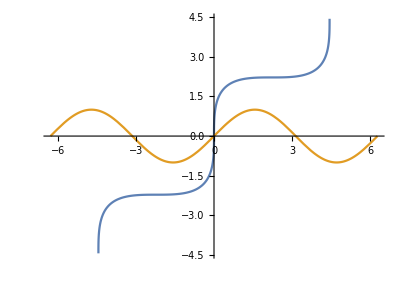

```mathematica
ParametricPlot[{
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},
{x,Sin[x]}
},{x,-2π,2π}]
```

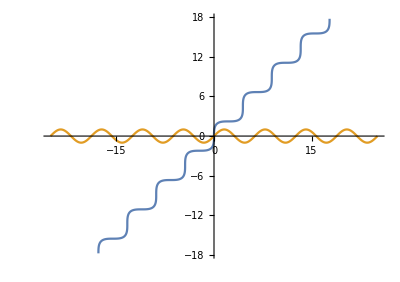

```mathematica
ParametricPlot[{
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},
{x,Sin[x]}
},{x,-8π,8π}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},
{x,Sin[x]},
{x,x-a}
},{x,-8π,8π}]
,{a,0,10}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},
{x,Sin[x]},
{x,-x-a}
},{x,-8π,8π}]
,{a,0,10}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},
{x,Sin[x]},
{x,-x-a}
},{x,-8π,8π}]
,{a,0,-10}]
```